## Notebook to accompany “Are the LIGO–Virgo observations the product of a single formation channel?”

Below we provide examples of how to calcualte the probabilities that the first n gravitational-wave events detected by come from a single formation channel, given a variety of assumptions about the rates for the different channels.

Code is provided for the scenarios we discuss in the accompanying paper; modifying these allows you to explore your own choice of scenario assumptions.

```mathematica
(* Working precesion for numerical integration *)
wp=10;
```

## Rate prior: log-normal distributions to approximate the measured total BBH merger rate (Abbott et al. 2017)

For most calcualtions, we assume that a unifrom prior (and uncorrelated) prior on the rates. The priors below allows us to test the impact of folding in information from LIGO and Virgo's measurement of the total merger rate.

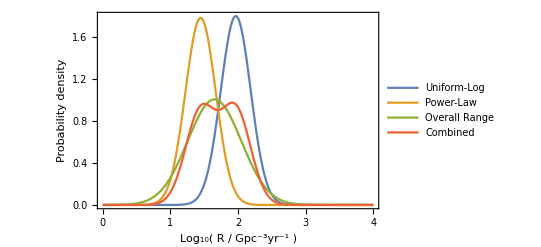

```mathematica
(* Uniform in log prior on mass ratio - 90% credible interval [12-65] Gpc^-3 yr^-1 *)
PosteriorOnTotalRateUniformLog[log10R_]:=Block[{μ=Log10[27.95],σ=Log10[1.673],ans},ⅇ^(-(log10R-μ)^2/(2 σ^2))/(√(2 π) σ)]

(* Power law prior on mass ratio - 90% credible interval [40-213] Gpc^-3 yr^-1 *)
PosteriorOnTotalRatePowerLaw[log10R_]:=Block[{μ=Log10[92.5],σ=Log10[1.665],ans},ⅇ^(-(log10R-μ)^2/(2 σ^2))/(√(2 π) σ)]

(* Approximate distribution for the overall range - 90% credible interval [10-200] Gpc^-3 yr^-1 *)
PosteriorOnTotalRateOverallRange[log10R_]:=Block[{μ=Log10[44.85],σ=Log10[2.49],ans},ⅇ^(-(log10R-μ)^2/(2 σ^2))/(√(2 π) σ)]

(* Sum - The sum of the two prior distributions with equal weights *)
PosteriorOnTotalRateCombined[log10R_]:=0.5*(PosteriorOnTotalRatePowerLaw[log10R]+PosteriorOnTotalRateUniformLog[log10R])

(* Plots of these distributions *)
Plot[{PosteriorOnTotalRatePowerLaw[logR],PosteriorOnTotalRateUniformLog[logR],PosteriorOnTotalRateOverallRange[logR],PosteriorOnTotalRateCombined[logR]},{logR,0,4},PlotRange->All,PlotLegends->{"Uniform-Log","Power-Law","Overall Range","Combined"},Frame->True,FrameLabel->{"Log_10( R / Gpc^-3yr^-1 )","Probability density"}]
```

The Overall range and Combined ranges give similar results. However, using either the uniform-in-log or the power-law ranges can give different results (try it out).

## Scenarios A and B

These are simple toy models to illustrate the effects of changing the range of uncertainty for the rates.

Scenario A: a highly uncertain scenario where the prior rate ranges are symmetric and span 6 orders of magnitude.

Scenario B: a moderately uncertain variant of scenario A; the two ranges are again symmetric but only span 2.5 orders of magnitude.

Here we compute P(n), P_1(n) and P_2(n) for these scenarios:
- P(n) = the probability that the first n events all come from the same channel (either 1 or 2)
- P_1(n) = the probability that the first n events all come from channel 1
- P_2(n) = the probability that the first n events all come from channel 2

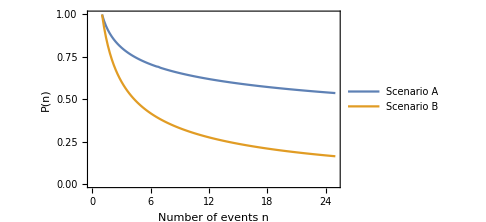

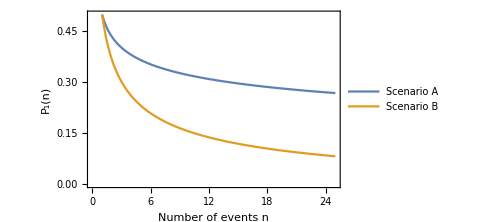
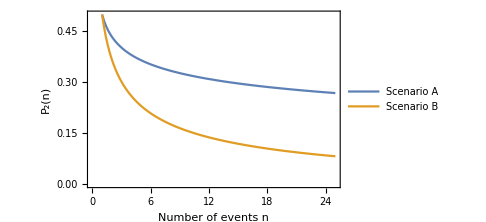
-Graphics- | -Graphics-

```mathematica
(* Scenario A: 6 orders of magnitude uncertainty on both rates *)
L=6;

(* Calculate probabilities by marginalising over the rates *)
PscenarioA=Table[{n,1/L^2 NIntegrate[(10^(n x)+10^(n y))/((10^(x)+10^(y))^n),{x,0,L},{y,0,L},WorkingPrecision->wp]},{n,1,25,0.2}];
P1scenarioA=Table[{n,1/L^2 NIntegrate[(10^x/(10^x+10^y))^n,{x,0,L},{y,0,L},WorkingPrecision->wp]},{n,1,25,0.2}];
P2scenarioA=Table[{n,1/L^2 NIntegrate[(10^y/(10^x+10^y))^n,{x,0,L},{y,0,L},WorkingPrecision->wp]},{n,1,25,0.2}];

(* Scenario B: 2.5 orders of magnitude uncertainty on both rates *)
L=2.5;

(* Calculate probabilities by marginalising over the rates *)
PscenarioB=Table[{n,1/L^2 NIntegrate[(10^(n x)+10^(n y))/((10^(x)+10^(y))^n),{x,0,L},{y,0,L},WorkingPrecision->wp]},{n,1,25,0.2}];
P1scenarioB=Table[{n,1/L^2 NIntegrate[(10^x/(10^x+10^y))^n,{x,0,L},{y,0,L},WorkingPrecision->wp]},{n,1,25,0.2}];
P2scenarioB=Table[{n,1/L^2 NIntegrate[(10^y/(10^x+10^y))^n,{x,0,L},{y,0,L},WorkingPrecision->wp]},{n,1,25,0.2}];

(* Plots *)
ListPlot[{PscenarioA,PscenarioB},Joined->True,Frame->True,FrameLabel->{"Number of events n","P(n)"},PlotLegends->{"Scenario A", "Scenario B"},ImageSize->Medium]

(* By symmetry the following pair of plots are identical in these scenarios - we include this for completeness *)
Grid[{{
ListPlot[{P1scenarioA,P1scenarioB},Joined->True,Frame->True,FrameLabel->{"Number of events n","P_1(n)"},PlotLegends->{"Scenario A", "Scenario B"},ImageSize->Medium],
ListPlot[{P2scenarioA,P2scenarioB},Joined->True,Frame->True,FrameLabel->{"Number of events n","P_2(n)"},PlotLegends->{"Scenario A", "Scenario B"},ImageSize->Medium]
}}]
```

Scenario A has a larger probability that all the events come from a single channel because of the larger prior uncertainty:there is more possibility that the rates are extremely different, meaning that one channel can dominate the other. For Scenario B, it is more probable that the two rates are similar, and so it is more probable that we observe a mixture of events from the two channels.

## Scenarios C and C’

These are simple approximations for the two best accepted potential formation channels, based upon different theoretical predictions.

Scenario C: modelled prior rate ranges from BEFORE the first detection.

Pre-detection theoretically modelled priors for the two leading candidate formation channels: field binaries [0.5,1000] Gpc^−3 yr&−1 (Mennekens & Vanbeveren 2014; Dominik et al. 2015), and dynamical formation [2, 20] Gpc^−3 yr^−1 (Ziosi et al. 2014; Rodriguez et al. 2016a), assuming that BBH do merge (otherwise we would never have n greater than 0). These rate estimates were taken from the literature published before the first GW detection to avoid the possibility of models being fine-tuned to accommodate observations.

Scenario C’: modelled prior rate ranges from AFTER the first detection. 

The same as Scenario C, but using the recent estimates for the prior ranges [7, 1300] Gpc^−3 yr^−1 (Belczynski et al. 2016; Eldridge & Stanway 2016) and [2, 40] Gpc^−3 yr^−1 (Rodriguez et al. 2016b; Askar et al. 2017) for the field and dynamical channels respectively.

Here we compute P(n), P_1(n) and P_2(n) for these scenarios:
- P(n) = the probability that the first n events all come from the same channel (either 1 or 2)
- P_1(n) = the probability that the first n events all come from channel 1
- P_2(n) = the probability that the first n events all come from channel 2

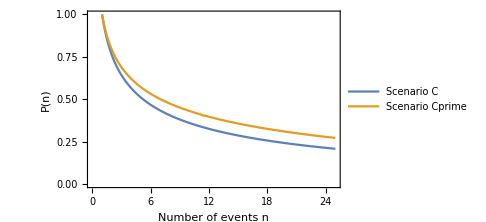

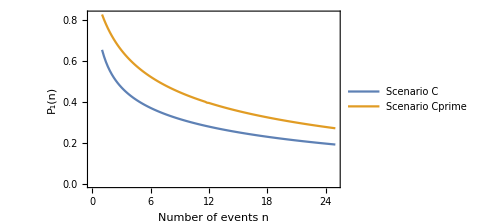
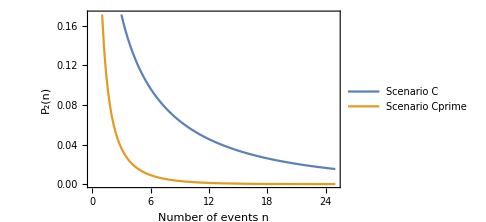
-Graphics- | -Graphics-

```mathematica
(* Scenario C *)
(* Isolated field binaries *)
top1=1000.0;
low1=0.5;

(* Dynamically formed binaries *)
top2=20.0;
low2=2.0;

L1=Log10[top1]-Log10[low1];
L2=Log10[top2]-Log10[low2];

(* Calculate probabilities by marginalising over the rates *)
PscenarioC=Table[{n,1/(L1 L2)NIntegrate[(10^(n x)+10^(n y))/((10^(x)+10^(y))^n),{x,Log10[low1],Log10[top1]},{y,Log10[low2],Log10[top2]},WorkingPrecision->wp]},{n,1,25,0.2}];
P1scenarioC=Table[{n,1/(L1 L2)NIntegrate[(10^x/(10^x+10^y))^n,{x,Log10[low1],Log10[top1]},{y,Log10[low2],Log10[top2]},WorkingPrecision->wp]},{n,1,25,0.2}];
P2scenarioC=Table[{n,1/(L1 L2)NIntegrate[(10^y/(10^x+10^y))^n,{x,Log10[low1],Log10[top1]},{y,Log10[low2],Log10[top2]},WorkingPrecision->wp]},{n,1,25,0.2}];

(* Scenario Cprime *)
(* Isolated fiedl binaries *)
top1=1300.0;
low1=7.0;

(* Dynamically formed binaries *)
top2=40.0;
low2=2.0;

L1=Log10[top1]-Log10[low1];
L2=Log10[top2]-Log10[low2];

(* Calculate probabilities by marginalising over the rates *)
PscenarioCprime=Table[{n,1/(L1 L2)NIntegrate[(10^(n x)+10^(n y))/((10^(x)+10^(y))^n),{x,Log10[low1],Log10[top1]},{y,Log10[low2],Log10[top2]},WorkingPrecision->wp]},{n,1,25,0.2}];
P1scenarioCprime=Table[{n,1/(L1 L2)NIntegrate[(10^x/(10^x+10^y))^n,{x,Log10[low1],Log10[top1]},{y,Log10[low2],Log10[top2]},WorkingPrecision->wp]},{n,1,25,0.2}];
P2scenarioCprime=Table[{n,1/(L1 L2)NIntegrate[(10^y/(10^x+10^y))^n,{x,Log10[low1],Log10[top1]},{y,Log10[low2],Log10[top2]},WorkingPrecision->wp]},{n,1,25,0.2}];

(* Plots *)
ListPlot[{PscenarioC,PscenarioCprime},Joined->True,Frame->True,FrameLabel->{"Number of events n","P(n)"},PlotLegends->{"Scenario C", "Scenario Cprime"},ImageSize->Medium]

Grid[{{
ListPlot[{P1scenarioC,P1scenarioCprime},Joined->True,Frame->True,FrameLabel->{"Number of events n","P_1(n)"},PlotLegends->{"Scenario C", "Scenario Cprime"},ImageSize->Medium],
ListPlot[{P2scenarioC,P2scenarioCprime},Joined->True,Frame->True,FrameLabel->{"Number of events n","P_2(n)"},PlotLegends->{"Scenario C", "Scenario Cprime"},ImageSize->Medium]
}}]
```

Scenario C and C’ have similar P(n), the change in rates don’t make much of a difference here. However, there is a significant difference in P_1(n) and P_2(n). This is an effect of the increase of the rate lower bound for the field channel (low1). If all the events come from a single channel, it is more probable that the come from the field channel, as the prior distribution on the rates extends much higher than for the dynamical formation channel. This shows that you need to be careful about drawing conclusions about which channel might be operating, because they can be sensitive to the prior assumptions that went into calcualting the range of possible rates.

## Scenario D

Here we test out the impact of changing our assumptions about how the two channels are correlated.

Scenario D: measured total BBH merger rate

The same as Scenario C, but incorporating a measurement for the total BBH merger rate (Abbott et al. 2017)

Here we compute P(n), P_1(n) and P_2(n) for these scenarios:
- P(n) = the probability that the first n events all come from the same channel (either 1 or 2)
- P_1(n) = the probability that the first n events all come from channel 1
- P_2(n) = the probability that the first n events all come from channel 2

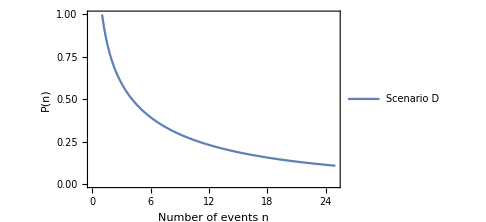

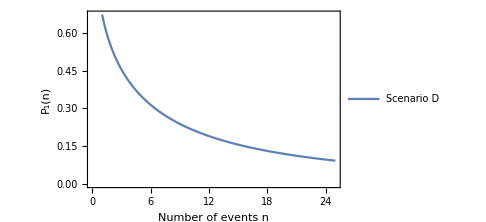
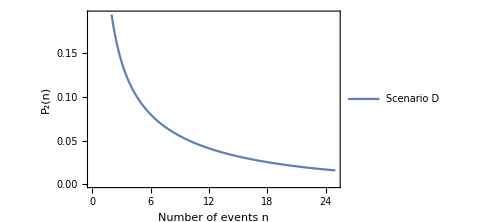
-Graphics- | -Graphics-

```mathematica
(* Scenario D: 2 formation channels, with non-trivial prior on total rate *)
(* Isolated field binaries *)
top1=1000.0;
low1=0.5;

(* Dynamically formed binaries *)
top2=20.0;
low2=2.0;

L1=Log10[top1]-Log10[low1];
L2=Log10[top2]-Log10[low2];

(* Weighting for the total rate based upon measured rates, here using a log-normal approximation to the total rate *)
(* Normalisation constant *)
priorvolume=NIntegrate[PosteriorOnTotalRateOverallRange[Log10[10^x+10^y]],{x,Log10[low1],Log10[top1]},{y,Log10[low2],Log10[top2]},WorkingPrecision->10];

(* Calculate probabilities by marginalising over the rates with prior weighting *)
PscenarioD=Table[{n,priorvolume^-1 NIntegrate[((10^(n x)+10^(n y))/((10^(x)+10^(y))^n))PosteriorOnTotalRateOverallRange[Log10[10^x+10^y]],{x,Log10[0.5],Log10[1000.]},{y,Log10[2.],Log10[20.]},WorkingPrecision->wp]},{n,1,25,0.2}];
P1scenarioD=Table[{n,priorvolume^-1 NIntegrate[(10^x/(10^x+10^y))^n PosteriorOnTotalRateOverallRange[Log10[10^x+10^y]],{x,Log10[0.5],Log10[1000.]},{y,Log10[2.],Log10[20.]},WorkingPrecision->wp]},{n,1,25,0.2}];
P2scenarioD=Table[{n,priorvolume^-1 NIntegrate[(10^y/(10^x+10^y))^n PosteriorOnTotalRateOverallRange[Log10[10^x+10^y]],{x,Log10[0.5],Log10[1000.]},{y,Log10[2.],Log10[20.]},WorkingPrecision->wp]},{n,1,25,0.2}];

(* Plots *)
ListPlot[{PscenarioD},Joined->True,Frame->True,FrameLabel->{"Number of events n","P(n)"},PlotLegends->{"Scenario D"},ImageSize->Medium]

Grid[{{
ListPlot[{P1scenarioD},Joined->True,Frame->True,FrameLabel->{"Number of events n","P_1(n)"},PlotLegends->{"Scenario D"},ImageSize->Medium],
ListPlot[{P2scenarioD},Joined->True,Frame->True,FrameLabel->{"Number of events n","P_2(n)"},PlotLegends->{"Scenario D"},ImageSize->Medium]
}}]
```

Scenario D: alternative distribution on total rates

We can repeat scenario D to examine the effect of switching from the Overall range distribution for the total merger rate to the Combined distribution: this is equivalent to marginalizing over the two possibilities [power-law and uniform-in-log] reported in Abbott et al. (2017) with equal prior weights.

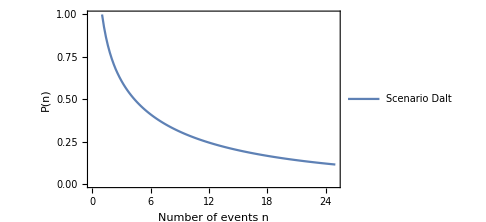

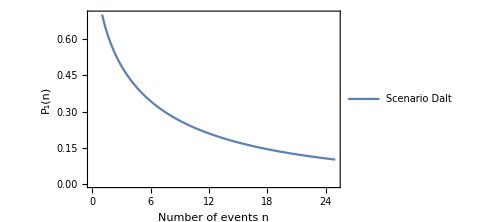
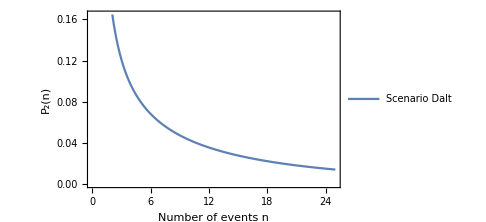
-Graphics- | -Graphics-

```mathematica
(* Scenario D: alternative distribution on total rates *)
(* Isolated field binaries *)
top1=1000.0;
low1=0.5;

(* Dynamically formed binaries *)
top2=20.0;
low2=2.0;

L1=Log10[top1]-Log10[low1];
L2=Log10[top2]-Log10[low2];

(* Weighting for the total rate based upon measured rates *)
(* Normalisation constant *)
priorvolume=NIntegrate[PosteriorOnTotalRateCombined[Log10[10^x+10^y]],{x,Log10[low1],Log10[top1]},{y,Log10[low2],Log10[top2]},WorkingPrecision->10];

(* Calculate probabilities by marginalising over the rates with prior weighting *)
PscenarioDalt=Table[{n,priorvolume^-1 NIntegrate[((10^(n x)+10^(n y))/((10^(x)+10^(y))^n))PosteriorOnTotalRateCombined[Log10[10^x+10^y]],{x,Log10[0.5],Log10[1000.]},{y,Log10[2.],Log10[20.]},WorkingPrecision->10]},{n,1,25,0.2}];
P1scenarioDalt=Table[{n,priorvolume^-1 NIntegrate[(10^x/(10^x+10^y))^n PosteriorOnTotalRateCombined[Log10[10^x+10^y]],{x,Log10[0.5],Log10[1000.]},{y,Log10[2.],Log10[20.]},WorkingPrecision->10]},{n,1,25,0.2}];
P2scenarioDalt=Table[{n,priorvolume^-1 NIntegrate[(10^y/(10^x+10^y))^n PosteriorOnTotalRateCombined[Log10[10^x+10^y]],{x,Log10[0.5],Log10[1000.]},{y,Log10[2.],Log10[20.]},WorkingPrecision->10]},{n,1,25,0.2}];

(* Plots *)
ListPlot[{PscenarioDalt},Joined->True,Frame->True,FrameLabel->{"Number of events n","P(n)"},PlotLegends->{"Scenario Dalt"},ImageSize->Medium]

Grid[{{
ListPlot[{P1scenarioDalt},Joined->True,Frame->True,FrameLabel->{"Number of events n","P_1(n)"},PlotLegends->{"Scenario Dalt"},ImageSize->Medium],
ListPlot[{P2scenarioDalt},Joined->True,Frame->True,FrameLabel->{"Number of events n","P_2(n)"},PlotLegends->{"Scenario Dalt"},ImageSize->Medium]
}}]
```

Results are similar using the Overall range and Combined priors, as expected.

However, changing the prior on the rates can have an impact on the various probabilities. For example, if the prior on the total rate is higher, it is more natural to explain events using the field channel (as that has rates which can extend to higher values), and so the probabilities that all the events come from the field channel increases realtive to the probability that they all come from the dynamical channel.

## Scenario E

Relaxing the assumptino that we have exactly two channels that operate.

Scenario E: additional more speculative formation channel(s)

The same as Scenario C, but allowing for additional formation channel(s). We assume that these (more speculative) channels only operate with probability ρ = 0.1; if they operate a highly uncertain prior on the combined additional rate R ≥ 3 spanning 10 orders of magnitude, with an upper limit set by the Initial LIGO–Virgo sixth science run (S6) bound is used (Aasi et al. 2013).

Here we compute P(n), P_1(n) and P_2(n) for these scenarios:
- P(n) = the probability that the first n events all come from the same channel (either 1 or 2)
- P_1(n) = the probability that the first n events all come from channel 1
- P_2(n) = the probability that the first n events all come from channel 2

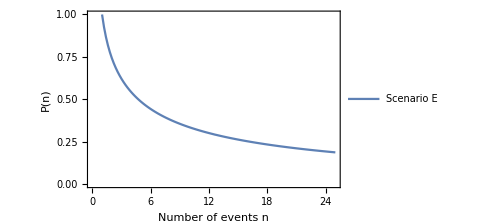

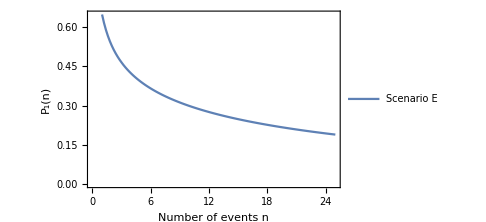
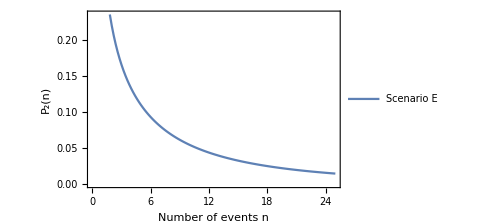
-Graphics- | -Graphics-

```mathematica
(* Scenario E: >3 formation channels, with probability ρ of >3rd operating *)
(* Isolated field binaries *)
top1=1000.0;
low1=0.5;

(* Dynamically formed binaries *)
top2=20.0;
low2=2.0;

L1=Log10[top1]-Log10[low1];
L2=Log10[top2]-Log10[low2];

(* Third, more speculative channel *)
upS6=Log10[900.]; (* This is the upper limit from S6 *)
ρ=0.1; (* Probability that the channel is in operation, set to 1 for a definite third channel *)
L3=10.;

(* Calculate probabilities by marginalising over the rates *)
PscenarioE=Table[{n,1/(L1 L2 L3)NIntegrate[(((ρ 10^x)/(10^x+10^y+10^z)+((1-ρ)10^x)/(10^x+10^y))^n+((ρ 10^y)/(10^x+10^y+10^z)+((1-ρ)10^y)/(10^x+10^y))^n+((ρ 10^z)/(10^x+10^y+10^z))^n),{x,Log10[0.5],Log10[1000.]},{y,Log10[2.],Log10[20.]},{z,upS6-L3,upS6},WorkingPrecision->wp]},{n,1,25,0.2}];
P1scenarioE=Table[{n,1/(L1 L2 L3)NIntegrate[(ρ(10^x/(10^x+10^y+10^z))^n+(1-ρ)(10^x/(10^x+10^y))^n),{x,Log10[0.5],Log10[1000.]},{y,Log10[2.],Log10[20.]},{z,upS6-L3,upS6},WorkingPrecision->wp]},{n,1,25,0.2}];
P2scenarioE=Table[{n,1/(L1 L2 L3)NIntegrate[(ρ(10^y/(10^x+10^y+10^z))^n+(1-ρ)(10^y/(10^x+10^y))^n),{x,Log10[0.5],Log10[1000.]},{y,Log10[2.],Log10[20.]},{z,upS6-L3,upS6},WorkingPrecision->wp]},{n,1,25,0.2}];

(* Plots *)
ListPlot[{PscenarioE},Joined->True,Frame->True,FrameLabel->{"Number of events n","P(n)"},PlotLegends->{"Scenario E"},ImageSize->Medium]

Grid[{{
ListPlot[{P1scenarioE},Joined->True,Frame->True,FrameLabel->{"Number of events n","P_1(n)"},PlotLegends->{"Scenario E"},ImageSize->Medium],
ListPlot[{P2scenarioE},Joined->True,Frame->True,FrameLabel->{"Number of events n","P_2(n)"},PlotLegends->{"Scenario E"},ImageSize->Medium]
}}]
```

Results here are similar to Scenario C. As ρ is made smaller, we get closer to Scenario C: the inclusion of highly speculative channels shouldn’t impact our conclusions. As ρ is made bigger, we see a larger impact. Introducing more channels should increases the probbability that we are seeing a mixture of different channels, as there are more possible ways for this to happen.

## Plotting summary results for all of the above scenarios

How to make Figure 2 from the accompanying paper

```mathematica
(* If you want the plots to have nice labels you will have to install MaTeX and evaluate this command... *)
<<MaTeX`
(* ... otherwise you can evaluate this instead which works but makes less nice figures *)
(* MaTeX[a_,b_]:=a *)
```

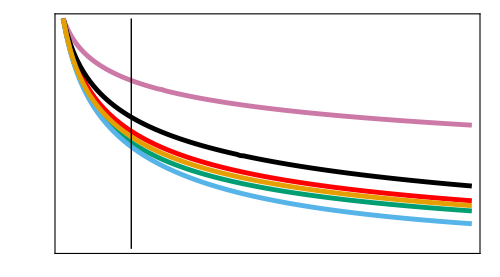
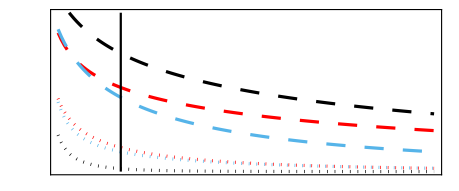
-Graphics-
-Graphics--Graphics--Graphics-

```mathematica
(* Set up nice axis tick marks *)
mag=1.75;
xticks=Table[{i,"",{0.016,0}},{i,1,25,5}]~Join~Table[{i,"",{0.008,0}},{i,1,25,1}];
xtickslabel={{5,MaTeX["5",Magnification->mag],{0.016,0}},{10,MaTeX["10",Magnification->mag],{0.016,0}},{15,MaTeX["15",Magnification->mag],{0.016,0}},{20,MaTeX["20",Magnification->mag],{0.016,0}},{25,MaTeX["25",Magnification->mag],{0.016,0}}}~Join~Table[{ i,"",{0.008,0}},{i,1,25,1}];
yticks=Table[{ i,"",{0.016,0}},{i,0,1,0.2}]~Join~Table[{i,"",{0.008,0}},{i,0,1,0.05}];
ytickslabel={{0,MaTeX["0.0",Magnification->mag],{0.016,0}},{0,MaTeX["0.0",Magnification->mag],{0.016,0}},{0.2,MaTeX["0.2",Magnification->mag],{0.016,0}},{0.4,MaTeX["0.4",Magnification->mag],{0.016,0}},{0.6,MaTeX["0.6",Magnification->mag],{0.016,0}},{0.8,MaTeX["0.8",Magnification->mag],{0.016,0}},{1.0,MaTeX["1.0",Magnification->mag],{0.016,0}}}~Join~Table[{i,"",{0.008,0}},{i,0,1,0.05}];
ytickslabelALT={{0.02,MaTeX["0.0",Magnification->mag],{0,0}},{0,"",{0.016,0}},{0.2,MaTeX["0.2",Magnification->mag],{0.016,0}},{0.4,MaTeX["0.4",Magnification->mag],{0.016,0}},{0.6,MaTeX["0.6",Magnification->mag],{0.016,0}},{0.8,MaTeX["0.8",Magnification->mag],{0.016,0}},{1.0,MaTeX["1.0",Magnification->mag],{0.016,0}}}~Join~Table[{i,"",{0.008,0}},{i,0,1,0.05}];

(* Colours, based upon the colour-blind palette from http://jfly.iam.u-tokyo.ac.jp/color/#pallet *)
cols={RGBColor[204/255,121/255,167/255],RGBColor[0,158/255,115/255],Red,Black,RGBColor[86/255,180/255,233/255],RGBColor[230/255,159/255,0]};

(* Plot legends *)
mag=2;
leg1=LineLegend[{{cols[[1]],Thickness[0.007]},{cols[[2]],Thickness[0.007]},{cols[[3]],Thickness[0.007]},Black},{MaTeX["\\textrm{ Scenario A}",Magnification->0.72mag],MaTeX["\\textrm{ Scenario B}",Magnification->0.72mag],MaTeX["\\textrm{ Scenario C}",Magnification->0.72mag]},LegendLayout->{"Column",1},Spacings->{0,-0.5},LegendMarkerSize->30];
leg2=LineLegend[{{cols[[4]],Thickness[0.007]},{cols[[5]],Thickness[0.007]},{cols[[6]],Thickness[0.007]},Black},{MaTeX["\\textrm{ Scenario C'}",Magnification->0.72mag],MaTeX["\\textrm{ Scenario D}",Magnification->0.72mag],MaTeX["\\textrm{ Scenario E}",Magnification->0.72mag]},LegendLayout->{"Column",1},Spacings->{0,-0.5},LegendMarkerSize->30];
leg3=LineLegend[{{Black,Thickness[0.005],Dashing[0.03]},{Black,Thickness[0.005],Dotted},Black},{MaTeX["\\;\\; P_{\\textrm{Field}}",Magnification->0.78mag],MaTeX["\\;\\; P_{\\textrm{Dynamic}}",Magnification->0.78mag]},LegendLayout->{"Column",1},Spacings->{0,-2.},LegendMarkerSize->54];

(* Plots *)
aspectratio=1./1.8;
topplot=ListPlot[{PscenarioA,PscenarioB,PscenarioC,PscenarioCprime,PscenarioD,PscenarioE,{{5,0},{5,1}}},Joined->True,Frame->True,AspectRatio->aspectratio,PlotStyle->{{cols[[1]],Thickness[0.007]},{cols[[2]],Thickness[0.007]},{cols[[3]],Thickness[0.007]},{cols[[4]],Thickness[0.007]},{cols[[5]],Thickness[0.007]},{cols[[6]],Thickness[0.007]},{Black,Thin}},FrameLabel->{None,MaTeX["P(n)",Magnification->0.95 mag]},ImageSize->500,PlotRange->{{1,25},{0,1}},PlotRangePadding->None,LabelStyle->Directive["Times",Black,14],PlotLegends->{Placed[leg1,Scaled[{0.52,0.82}]],Placed[leg2,Scaled[{0.84,0.82}]]},FrameTicks->{{ytickslabelALT,yticks},{xticks,xticks}},ImagePadding->{{70,9},{1,10}}];
bottomplot=Labeled[ListPlot[{P1scenarioC,P1scenarioCprime,P1scenarioD,P2scenarioC,P2scenarioCprime,P2scenarioD,{{5,0},{5,1}}},Joined->True,Frame->True,AspectRatio->0.75aspectratio,PlotStyle->{{cols[[3]],Thickness[0.005],Dashing[0.03]},{cols[[4]],Thickness[0.005],Dashing[0.03]},{cols[[5]],Thickness[0.005],Dashing[0.03]},{cols[[3]],Thickness[0.005],Dotted},{cols[[4]],Thickness[0.005],Dotted},{cols[[5]],Thickness[0.005],Dotted},{Black,Thin}},ImageSize->460,PlotRange->{{1,25},{0,0.75}},PlotRangePadding->None,LabelStyle->Directive["Times",Black,14],PlotLegends->Placed[leg3,Scaled[{0.82,0.8}]],FrameTicks->{{ytickslabel,yticks},{xtickslabel,xticks}},ImagePadding->{{30,9},{24,1}}],{MaTeX["\\hspace{0.45cm}\\textrm{Number of Events }n",Magnification->0.95mag],MaTeX["P_{i}(n)",Magnification->0.95mag]},{Bottom,Left},RotateLabel->True];

(* Final Plot *)
plot=Grid[{{topplot},{bottomplot}},Spacings->{0,0.1}]
```

## Scenario F

Here and in Scenario F’, we relax the assumption that the have to be multiple channels operating.

Scenario F: the possibility of only one channel definitely operating (Dynamical channel)

The same as Scenario C, but allowing for the possibility that only one channel operates. Here we assume that the field binary channel only operates with probability ρ = 0.1. We know that binaries of compact objects do form via isolated evolution, so this example is more of an illustration. The scenario might be applicable if it is not the case that binaries formed through isolated evolution are close enough to merge in a Hubble time, but this could be more naturally described by using a very low rate in Scenario C.

Here we compute P(n), P_1(n) and P_2(n) for these scenarios:
- P(n) = the probability that the first n events all come from the same channel (either 1 or 2)
- P_1(n) = the probability that the first n events all come from channel 1
- P_2(n) = the probability that the first n events all come from channel 2

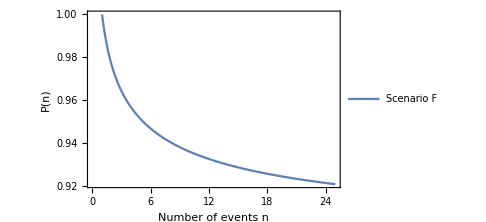

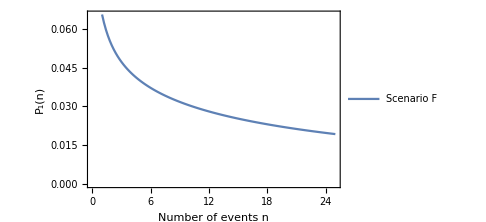
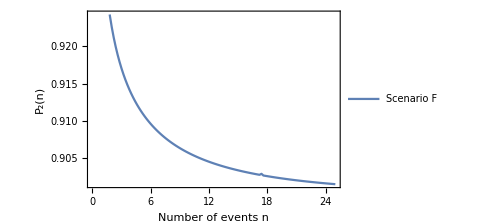
-Graphics- | -Graphics-

```mathematica
(* Scenario F: probability ρ of field channel operating *)
ρ=0.1; (* Set to 1 to recover Scenario C *)

(* Isolated field binaries *)
top1=1000.0;
low1=0.5;

(* Dynamically formed binaries *)
top2=20.0;
low2=2.0;

L1=Log10[top1]-Log10[low1];
L2=Log10[top2]-Log10[low2];

(* Calculate probabilities by marginalising over the rates *)
PscenarioF=Table[{n,1/(L1 L2)NIntegrate[(ρ(10^x/(10^x+10^y))^n)+(ρ(10^y/(10^x+10^y))^n+(1-ρ)),{x,Log10[0.5],Log10[1000.]},{y,Log10[2.],Log10[20.]},WorkingPrecision->16]},{n,1,25,0.2}];
P1scenarioF=Table[{n,1/(L1 L2)NIntegrate[(ρ(10^x/(10^x+10^y))^n),{x,Log10[0.5],Log10[1000.]},{y,Log10[2.],Log10[20.]},WorkingPrecision->16]},{n,1,25,0.2}];
P2scenarioF=Table[{n,1/(L1 L2)NIntegrate[(ρ(10^y/(10^x+10^y))^n+(1-ρ)),{x,Log10[0.5],Log10[1000.]},{y,Log10[2.],Log10[20.]},WorkingPrecision->16]},{n,1,25,0.2}];

(* Plots *)
ListPlot[{PscenarioF},Joined->True,Frame->True,FrameLabel->{"Number of events n","P(n)"},PlotLegends->{"Scenario F"},ImageSize->Medium]

Grid[{{
ListPlot[{P1scenarioF},Joined->True,Frame->True,FrameLabel->{"Number of events n","P_1(n)"},PlotLegends->{"Scenario F"},ImageSize->Medium],
ListPlot[{P2scenarioF},Joined->True,Frame->True,FrameLabel->{"Number of events n","P_2(n)"},PlotLegends->{"Scenario F"},ImageSize->Medium]
}}]
```

As expected, in this case it is much more probable that the definite channel dominates. As ρ tends towards zero, it would become a certainty that only one channel accounts for all the events.

## Scenario F’

THe complement of Scenario F, where we swap the definite and uncertain channel.  The calcualtion is the same as for Scenario F, but switched for the other channel to illustrate the effect.

Scenario F’: the possibility of only one channel definitely operating (Field binary channel)

The same as Scenario C, but allowing for the possibility that only one channel operates. Here we assume that the dynamical channel only operates with probability ρ = 0.1. Again, we know that binaries form dynamically, so this example is more of an illustration.

Here we compute P(n), P_1(n) and P_2(n) for these scenarios:
- P(n) = the probability that the first n events all come from the same channel (either 1 or 2)
- P_1(n) = the probability that the first n events all come from channel 1
- P_2(n) = the probability that the first n events all come from channel 2

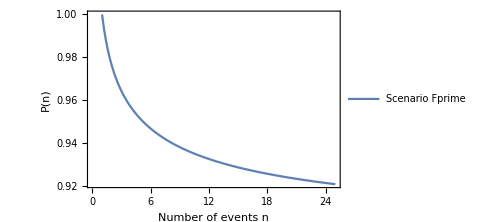

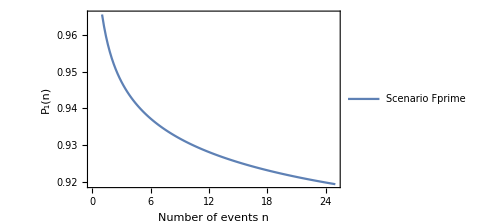
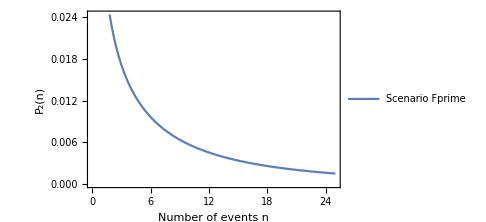
-Graphics- | -Graphics-

```mathematica
(* Scenario Fprime: probability ρ of dynamical channel operating *)
ρ=0.1; (* Set to 1 to recover Scenario C *)

(* Isolated field binaries *)
top1=1000.0;
low1=0.5;

(* Dynamically formed binaries *)
top2=20.0;
low2=2.0;

L1=Log10[top1]-Log10[low1];
L2=Log10[top2]-Log10[low2];

(* Calculate probabilities by marginalising over the rates *)
PscenarioFprime=Table[{n,1/(L1 L2)NIntegrate[(ρ(10^x/(10^x+10^y))^n+(1-ρ))+(ρ(10^y/(10^x+10^y))^n),{x,Log10[0.5],Log10[1000.]},{y,Log10[2.],Log10[20.]},WorkingPrecision->16]},{n,1,25,0.2}];
P1scenarioFprime=Table[{n,1/(L1 L2)NIntegrate[(ρ(10^x/(10^x+10^y))^n+(1-ρ)),{x,Log10[0.5],Log10[1000.]},{y,Log10[2.],Log10[20.]},WorkingPrecision->16]},{n,1,25,0.2}];
P2scenarioFprime=Table[{n,1/(L1 L2)NIntegrate[(ρ(10^y/(10^x+10^y))^n),{x,Log10[0.5],Log10[1000.]},{y,Log10[2.],Log10[20.]},WorkingPrecision->16]},{n,1,25,0.2}];

(* Plots *)
ListPlot[{PscenarioFprime},Joined->True,Frame->True,FrameLabel->{"Number of events n","P(n)"},PlotLegends->{"Scenario Fprime"},ImageSize->Medium]

Grid[{{
ListPlot[{P1scenarioFprime},Joined->True,Frame->True,FrameLabel->{"Number of events n","P_1(n)"},PlotLegends->{"Scenario Fprime"},ImageSize->Medium],
ListPlot[{P2scenarioFprime},Joined->True,Frame->True,FrameLabel->{"Number of events n","P_2(n)"},PlotLegends->{"Scenario Fprime"},ImageSize->Medium]
}}]
```

As with Scenario F, the definite channel dominates the probability. Here the difference is even larger becasue of the difference in rates as well.

## Miscellaneous

Add your own code here!

```mathematica
(*outputPath="ENTER PATH HERE";
Export[outputPath,plot]*)
```

## References

LIGO–Virgo papers

Pre-detection rates review
Abadie et al. (2010); arXiv:1003.2480

S6 BBH search and upper limits
Aasi et al. (2013); arXiv:1209.6533

Summary of first observing run (O1) and the first BBH discoveries GW150914, LVT151012 and GW151226
Abbott et al. (2016a); arXiv:1606.04856

Discovery of GW170104 and most recent BBH merger rates (at time of writing)
Abbott et al. (2017); arXiv:1706.01812

Discovery of GW170814 (which brings n to ~5)
Abbott et al. (2017a); arXiv:1709.09660

Rate prediction papers

Pre-detection rates
Isolated field binaries
Mennekins & Vanbeveren (2014); arXiv:1307.0959
Dominik et al. (2015); arXiv:1405.7016
Dynamical formed binaries
Ziosi et al. (2014); arXiv:1404.7147
Rodriguez et al. (2016a); arXiv:1602.02444

Post-detection rates
Isolated field binaries
Belczynski et al. (2016); arXiv:1602.04531
Eldridge & Stanway (2016); arXiv:1602.03790
Dynamically formed binaries
Rodriguez et al (2016b); arXiv:1604.04254
Askar et al. (2017); arXiv:1608.02520